```mathematica
optsLabel1=Sequence[FontFamily->"Helvetica",FontSize->22];
optsLabel2=Sequence[FontFamily->"Helvetica",FontSize->22,Transparent];
optsCentrality=Sequence[FontFamily->"Helvetica",FontSize->18];
optsCentrality2=Sequence[FontFamily->"Helvetica",FontSize->18,Transparent];
optsScale1=Sequence[FontFamily->"Helvetica",FontSize->16];
optsScale2=Sequence[FontFamily->"Helvetica",FontSize->16,Transparent];
```

```mathematica
Clear[c,ct,α,ω,p,s,ϕMC,KRC,γ,αc,αM,M,R]
```

```mathematica
c=αc/4(√(1+(8ct)/αc)-1)
```

1/4 (-1+√(1+(8 ct)/αc)) αc

```mathematica
M=αM/4(√(1+(8Mt)/αM)-1)
```

1/4 (-1+√(1+(8 Mt)/αM)) αM

Equation for Mt, we solve for zero (Eq. 15 in the mansucript):  Mt-(r1*phi)/((αM/4(√(1+(8Mt)/αM)-1))^2+1)=0

```mathematica
αc=5. √2
ω=3000.
p=20.
s=0.0043
αM=2. √5
phi=0.2
```

7.07107

3000.

20.

0.0043

4.47214

0.2

```mathematica
Clear[r1]
```

```mathematica
rr=Table[{r1,NSolve[-ct/r1+s+((-1+√(1+(8 ct)/αc))^2 αc^2)/(16 (1+1/16 (1+1/p) (-1+√(1+(8 ct)/αc))^2 αc^2+((-1+√(1+(8 ct)/αc))^4 αc^4 ω)/(256 p)))==0,ct,Reals]},{r1,4,10.3,0.1}]
```

{{4.,{{ct→0.0185636}}},{4.1,{{ct→0.0191109}}},{4.2,{{ct→0.0196658}}},{4.3,{{ct→0.020229}}},{4.4,{{ct→0.0208008}}},{4.5,{{ct→0.0213818}}},{4.6,{{ct→0.0219725}}},{4.7,{{ct→0.0225735}}},{4.8,{{ct→0.0231855}}},{4.9,{{ct→0.0238092}}},{5.,{{ct→0.0244453}}},{5.1,{{ct→0.0250946}}},{5.2,{{ct→0.0257582}}},{5.3,{{ct→0.026437}}},{5.4,{{ct→0.027132}}},{5.5,{{ct→0.0278447}}},{5.6,{{ct→0.0285763}}},{5.7,{{ct→0.0293284}}},{5.8,{{ct→0.0301027}}},{5.9,{{ct→0.0309013}}},{6.,{{ct→0.0317263},{ct→0.190456},{ct→0.229851}}},{6.1,{{ct→0.0325804},{ct→0.175697},{ct→0.244948}}},{6.2,{{ct→0.0334665},{ct→0.165626},{ct→0.255328}}},{6.3,{{ct→0.0343882},{ct→0.157448},{ct→0.263781}}},{6.4,{{ct→0.0353495},{ct→0.150361},{ct→0.271106}}},{6.5,{{ct→0.0363553},{ct→0.143997},{ct→0.277666}}},{6.6,{{ct→0.0374115},{ct→0.138148},{ct→0.283662}}},{6.7,{{ct→0.0385252},{ct→0.13268},{ct→0.289222}}},{6.8,{{ct→0.0397054},{ct→0.127499},{ct→0.294429}}},{6.9,{{ct→0.0409635},{ct→0.122533},{ct→0.299345}}},{7.,{{ct→0.0423139},{ct→0.117724},{ct→0.304015}}},{7.1,{{ct→0.0437765},{ct→0.113015},{ct→0.308471}}},{7.2,{{ct→0.0453782},{ct→0.108354},{ct→0.312743}}},{7.3,{{ct→0.0471585},{ct→0.103679},{ct→0.316851}}},{7.4,{{ct→0.0491786},{ct→0.0989114},{ct→0.320813}}},{7.5,{{ct→0.0515426},{ct→0.0939314},{ct→0.324644}}},{7.6,{{ct→0.054456},{ct→0.0885212},{ct→0.328357}}},{7.7,{{ct→0.0584582},{ct→0.0821308},{ct→0.331961}}},{7.8,{{ct→0.335467}}},{7.9,{{ct→0.338881}}},{8.,{{ct→0.342211}}},{8.1,{{ct→0.345463}}},{8.2,{{ct→0.348642}}},{8.3,{{ct→0.351753}}},{8.4,{{ct→0.3548}}},{8.5,{{ct→0.357787}}},{8.6,{{ct→0.360718}}},{8.7,{{ct→0.363595}}},{8.8,{{ct→0.366422}}},{8.9,{{ct→0.369201}}},{9.,{{ct→0.371935}}},{9.1,{{ct→0.374625}}},{9.2,{{ct→0.377274}}},{9.3,{{ct→0.379883}}},{9.4,{{ct→0.382455}}},{9.5,{{ct→0.384991}}},{9.6,{{ct→0.387492}}},{9.7,{{ct→0.38996}}},{9.8,{{ct→0.392397}}},{9.9,{{ct→0.394802}}},{10.,{{ct→0.397178}}},{10.1,{{ct→0.399526}}},{10.2,{{ct→0.401847}}},{10.3,{{ct→0.404141}}}}

```mathematica
rr=Table[{r1,NSolve[-ct/r1+s+((-1+√(1+(8 ct)/αc))^2 αc^2)/(16 (1+1/16 (1+1/p) (-1+√(1+(8 ct)/αc))^2 αc^2+((-1+√(1+(8 ct)/αc))^4 αc^4 ω)/(256 p)))==0,ct,Reals]},{r1,5.91, 5.99,0.01}]
```

{{5.91,{{ct→0.0309826}}},{5.92,{{ct→0.0310641}}},{5.93,{{ct→0.0311459}}},{5.94,{{ct→0.031228}}},{5.95,{{ct→0.0313103}}},{5.96,{{ct→0.031393},{ct→0.202083},{ct→0.218081}}},{5.97,{{ct→0.0314759},{ct→0.19806},{ct→0.22214}}},{5.98,{{ct→0.0315591},{ct→0.195086},{ct→0.22515}}},{5.99,{{ct→0.0316425},{ct→0.192616},{ct→0.227656}}}}

```mathematica
rr=Table[{r1,NSolve[-ct/r1+s+((-1+√(1+(8 ct)/αc))^2 αc^2)/(16 (1+1/16 (1+1/p) (-1+√(1+(8 ct)/αc))^2 αc^2+((-1+√(1+(8 ct)/αc))^4 αc^4 ω)/(256 p)))==0,ct,Reals]},{r1,7.61, 7.79,0.01}]
```

{{7.61,{{ct→0.0547923},{ct→0.0879414},{ct→0.328722}}},{7.62,{{ct→0.0551394},{ct→0.0873518},{ct→0.329086}}},{7.63,{{ct→0.0554982},{ct→0.0867516},{ct→0.329449}}},{7.64,{{ct→0.0558698},{ct→0.0861396},{ct→0.329811}}},{7.65,{{ct→0.0562555},{ct→0.0855146},{ct→0.330172}}},{7.66,{{ct→0.0566567},{ct→0.0848751},{ct→0.330532}}},{7.67,{{ct→0.0570753},{ct→0.0842194},{ct→0.330891}}},{7.68,{{ct→0.0575132},{ct→0.0835452},{ct→0.331248}}},{7.69,{{ct→0.0579732},{ct→0.0828501},{ct→0.331605}}},{7.7,{{ct→0.0584582},{ct→0.0821308},{ct→0.331961}}},{7.71,{{ct→0.0589724},{ct→0.0813834},{ct→0.332316}}},{7.72,{{ct→0.059521},{ct→0.0806026},{ct→0.33267}}},{7.73,{{ct→0.0601107},{ct→0.0797817},{ct→0.333023}}},{7.74,{{ct→0.0607511},{ct→0.0789109},{ct→0.333375}}},{7.75,{{ct→0.0614561},{ct→0.0779766},{ct→0.333726}}},{7.76,{{ct→0.0622471},{ct→0.0769573},{ct→0.334076}}},{7.77,{{ct→0.0631607},{ct→0.0758163},{ct→0.334425}}},{7.78,{{ct→0.0642701},{ct→0.0744804},{ct→0.334773}}},{7.79,{{ct→0.0657754},{ct→0.0727496},{ct→0.33512}}}}

From the above tables, we manually extract solutions corresponding to the lower, intermediate, and higher branches. Further, we select KRC such that the M/R ratio starts at 1; however, this is a free parameter and does not affect the dynamics.

```mathematica
rrDown={{4.,0.01856363401849362},{4.1,0.01911085859130647},{4.2,0.019665824718615915},{4.3,0.020228975662459292},{4.4,0.02080078710368071},{4.5,0.021381770696306007},{4.6,0.02197247812147844},{4.7,0.02257350572931875},{4.8,0.02318549987603146},{4.9,0.023809163087376708},{5.,0.02444526120970845},{5.1,0.02509463174809098},{5.2,0.025758193640187308},{5.3,0.026436958778291136},{5.4,0.02713204567507724},{5.5,0.02784469577843261},{5.6,0.028576293087136186},{5.7,0.02932838791663439},{5.8,0.03010272593384886},{5.9,0.030901283953249002},{5.91,0.030982555911104395},{5.92,0.031064094741623728},{5.93,0.0311459028977596},{5.94,0.031227982866676048},{5.95,0.03131033717041079},{5.96,0.03139296836655385},{5.97,0.031475879048943084},{5.98,0.03155907184837714},{5.99,0.03164254943334633},{6.,0.03172631451078205},{6.1,0.03258040198077962},{6.2,0.033466534088630345},{6.300000000000001,0.034388194283865456},{6.4,0.03534948287985189},{6.5,0.03635527865647655},{6.6,0.037411458671277084},{6.7,0.03852520398803726},{6.800000000000001,0.039705436049044696},{6.9,0.040963458733047624},{7.,0.042313937899375584},{7.1,0.04377646300236218},{7.2,0.04537817639789295},{7.300000000000001,0.047158520434161},{7.4,0.049178641442084156},{7.5,0.05154261405494489},{7.6,0.05445596482340252},{7.61,0.05479228414086877},{7.62,0.055139379427651784},{7.63,0.055498194241148685},{7.640000000000001,0.05586981543244957},{7.65,0.05625550543382878},{7.66,0.05665674452942836},{7.67,0.05707528715889945},{7.680000000000001,0.05751323840032083},{7.69,0.057973160236761676},{7.7,0.058458223128349446},{7.71,0.05897242898117693},{7.720000000000001,0.05952095146248424},{7.73,0.06011067925752208},{7.74,0.06075113313525173},{7.75,0.06145612914295898},{7.760000000000001,0.06224709834173169},{7.7700000000000005,0.06316067624666764},{7.78,0.06427013329768222},{7.79,0.06577538802822197}};
```

```mathematica
rrMiddle={{5.96,0.2020831203924559},{5.97,0.19806000382453706},{5.98,0.19508617485239357},{5.99,0.19261551997356113},{6.,0.19045633932440234},{6.1,0.17569720033467945},{6.2,0.1656256593189646},{6.300000000000001,0.1574477339933924},{6.4,0.15036100082175408},{6.5,0.14399696538115345},{6.6,0.1381476047461974},{6.7,0.13267953384759484},{6.800000000000001,0.12749874020459528},{6.9,0.12253330306849926},{7.,0.11772354749597765},{7.1,0.11301536405590556},{7.2,0.10835443694692963},{7.300000000000001,0.10367947094607566},{7.4,0.0989114282848712},{7.5,0.09393136186849406},{7.6,0.08852121959887845},{7.61,0.08794135804064479},{7.62,0.08735179584866946},{7.63,0.08675157983736277},{7.640000000000001,0.08613961366894378},{7.65,0.08551462556303029},{7.66,0.0848751260231136},{7.67,0.08421935153015014},{7.680000000000001,0.08354518805694826},{7.69,0.0828500647989807},{7.7,0.08213080259975993},{7.71,0.08138339097943977},{7.720000000000001,0.08060264781720583},{7.73,0.07978167609204628},{7.74,0.07891094681474564},{7.75,0.07797663583102245},{7.760000000000001,0.07695730408385959},{7.7700000000000005,0.07581630817115859},{7.78,0.074480369872847},{7.79,0.07274956298013106}};
```

```mathematica
rrUp={{5.96,0.21808113874089044},{5.97,0.22214031650795227},{5.98,0.22514995278466865},{5.99,0.22765615823189075},{6.,0.2298506298336595},{6.1,0.24494773721231883},{6.2,0.25532780310787223},{6.300000000000001,0.2637811612073517},{6.4,0.2711059741032041},{6.5,0.27766570128530166},{6.6,0.2836623368994478},{6.7,0.2892219376081479},{6.800000000000001,0.2944294514286416},{6.9,0.2993453564695185},{7.,0.3040145272472677},{7.1,0.30847135329543857},{7.2,0.31274288166785463},{7.300000000000001,0.3168508428239438},{7.4,0.3208130096846777},{7.5,0.32464414001443603},{7.6,0.32835664840207696},{7.7,0.3319610970410908},{7.800000000000001,0.3354665616856382},{7.9,0.33888090953080685},{8.,0.3422110136241129},{8.100000000000001,0.34546292068009005},{8.2,0.34864198411169056},{8.3,0.351752970707175},{8.4,0.3548001470683437},{8.5,0.3577873503159519},{8.600000000000001,0.3607180464282824},{8.7,0.36359537875932735},{8.8,0.3664222086854846},{8.9,0.36920114988832636},{9.,0.371934597451119},{9.100000000000001,0.37462475269749423},{9.2,0.37727364451036993},{9.3,0.37988314772256393},{9.4,0.3824549990565206},{9.5,0.38499081100119076},{9.600000000000001,0.3874920839434952},{9.7,0.3899602168156205},{9.8,0.3923965164743838},{9.9,0.39480220599261556},{10.,0.39717843201306813},{10.100000000000001,0.39952627129134455},{10.2,0.40184673653464253},{10.3,0.40414078162686756}}
```

{{5.96,0.218081},{5.97,0.22214},{5.98,0.22515},{5.99,0.227656},{6.,0.229851},{6.1,0.244948},{6.2,0.255328},{6.3,0.263781},{6.4,0.271106},{6.5,0.277666},{6.6,0.283662},{6.7,0.289222},{6.8,0.294429},{6.9,0.299345},{7.,0.304015},{7.1,0.308471},{7.2,0.312743},{7.3,0.316851},{7.4,0.320813},{7.5,0.324644},{7.6,0.328357},{7.7,0.331961},{7.8,0.335467},{7.9,0.338881},{8.,0.342211},{8.1,0.345463},{8.2,0.348642},{8.3,0.351753},{8.4,0.3548},{8.5,0.357787},{8.6,0.360718},{8.7,0.363595},{8.8,0.366422},{8.9,0.369201},{9.,0.371935},{9.1,0.374625},{9.2,0.377274},{9.3,0.379883},{9.4,0.382455},{9.5,0.384991},{9.6,0.387492},{9.7,0.38996},{9.8,0.392397},{9.9,0.394802},{10.,0.397178},{10.1,0.399526},{10.2,0.401847},{10.3,0.404141}}

```mathematica
NMaxDown=Length[rrDown]
NMaxMiddle=Length[rrMiddle]
NMaxUp=Length[rrUp]
```

65

40

48

```mathematica
KRC=0.63264093282842/0.01856363401849362
```

34.0796

```mathematica
RDown=Table[{rrDown[[i,1]],KRC*rrDown[[i,2]]},{i,1,NMaxDown}]
```

{{4.,0.632641},{4.1,0.65129},{4.2,0.670203},{4.3,0.689395},{4.4,0.708882},{4.5,0.728682},{4.6,0.748813},{4.7,0.769296},{4.8,0.790152},{4.9,0.811406},{5.,0.833084},{5.1,0.855215},{5.2,0.877829},{5.3,0.900961},{5.4,0.924649},{5.5,0.948936},{5.6,0.973868},{5.7,0.999499},{5.8,1.02589},{5.9,1.0531},{5.91,1.05587},{5.92,1.05865},{5.93,1.06144},{5.94,1.06424},{5.95,1.06704},{5.96,1.06986},{5.97,1.07268},{5.98,1.07552},{5.99,1.07836},{6.,1.08122},{6.1,1.11033},{6.2,1.14053},{6.3,1.17194},{6.4,1.2047},{6.5,1.23897},{6.6,1.27497},{6.7,1.31292},{6.8,1.35314},{6.9,1.39602},{7.,1.44204},{7.1,1.49188},{7.2,1.54647},{7.3,1.60714},{7.4,1.67599},{7.5,1.75655},{7.6,1.85584},{7.61,1.8673},{7.62,1.87913},{7.63,1.89136},{7.64,1.90402},{7.65,1.91716},{7.66,1.93084},{7.67,1.9451},{7.68,1.96003},{7.69,1.9757},{7.7,1.99223},{7.71,2.00976},{7.72,2.02845},{7.73,2.04855},{7.74,2.07037},{7.75,2.0944},{7.76,2.12136},{7.77,2.15249},{7.78,2.1903},{7.79,2.2416}}

```mathematica
RMiddle=Table[{rrMiddle[[i,1]],KRC*rrMiddle[[i,2]]},{i,1,NMaxMiddle}]
```

{{5.96,6.88691},{5.97,6.7498},{5.98,6.64846},{5.99,6.56426},{6.,6.49067},{6.1,5.98769},{6.2,5.64445},{6.3,5.36575},{6.4,5.12424},{6.5,4.90736},{6.6,4.70801},{6.7,4.52166},{6.8,4.3451},{6.9,4.17588},{7.,4.01197},{7.1,3.85152},{7.2,3.69267},{7.3,3.53335},{7.4,3.37086},{7.5,3.20114},{7.6,3.01677},{7.61,2.997},{7.62,2.97691},{7.63,2.95646},{7.64,2.9356},{7.65,2.9143},{7.66,2.89251},{7.67,2.87016},{7.68,2.84719},{7.69,2.8235},{7.7,2.79898},{7.71,2.77351},{7.72,2.7469},{7.73,2.71893},{7.74,2.68925},{7.75,2.65741},{7.76,2.62267},{7.77,2.58379},{7.78,2.53826},{7.79,2.47927}}

```mathematica
RUp=Table[{rrUp[[i,1]],KRC*rrUp[[i,2]]},{i,1,NMaxUp}]
```

{{5.96,7.43211},{5.97,7.57045},{5.98,7.67302},{5.99,7.75843},{6.,7.83321},{6.1,8.34772},{6.2,8.70147},{6.3,8.98955},{6.4,9.23918},{6.5,9.46273},{6.6,9.66709},{6.7,9.85656},{6.8,10.034},{6.9,10.2016},{7.,10.3607},{7.1,10.5126},{7.2,10.6581},{7.3,10.7981},{7.4,10.9332},{7.5,11.0637},{7.6,11.1903},{7.7,11.3131},{7.8,11.4326},{7.9,11.5489},{8.,11.6624},{8.1,11.7732},{8.2,11.8816},{8.3,11.9876},{8.4,12.0914},{8.5,12.1932},{8.6,12.2931},{8.7,12.3912},{8.8,12.4875},{8.9,12.5822},{9.,12.6754},{9.1,12.7671},{9.2,12.8573},{9.3,12.9463},{9.4,13.0339},{9.5,13.1203},{9.6,13.2056},{9.7,13.2897},{9.8,13.3727},{9.9,13.4547},{10.,13.5357},{10.1,13.6157},{10.2,13.6948},{10.3,13.7729}}

```mathematica
mm=Table[{r1,NSolve[Mt-(phi r1)/((αM/4(√(1+(8Mt)/αM)-1))^2+1)==0,Mt,Reals]},{r1,4, 5.96,0.1}]
```

{{4.,{{Mt→0.632641}}},{4.1,{{Mt→0.644263}}},{4.2,{{Mt→0.655744}}},{4.3,{{Mt→0.667088}}},{4.4,{{Mt→0.678298}}},{4.5,{{Mt→0.689378}}},{4.6,{{Mt→0.700331}}},{4.7,{{Mt→0.711162}}},{4.8,{{Mt→0.721872}}},{4.9,{{Mt→0.732466}}},{5.,{{Mt→0.742945}}},{5.1,{{Mt→0.753314}}},{5.2,{{Mt→0.763575}}},{5.3,{{Mt→0.77373}}},{5.4,{{Mt→0.783782}}},{5.5,{{Mt→0.793733}}},{5.6,{{Mt→0.803587}}},{5.7,{{Mt→0.813345}}},{5.8,{{Mt→0.823009}}},{5.9,{{Mt→0.832582}}}}

```mathematica
mm=Table[{r1,NSolve[Mt-(phi r1)/((αM/4(√(1+(8Mt)/αM)-1))^2+1)==0,Mt,Reals]},{r1,5.91, 5.99,0.01}]
```

{{5.91,{{Mt→0.833535}}},{5.92,{{Mt→0.834486}}},{5.93,{{Mt→0.835437}}},{5.94,{{Mt→0.836386}}},{5.95,{{Mt→0.837335}}},{5.96,{{Mt→0.838283}}},{5.97,{{Mt→0.83923}}},{5.98,{{Mt→0.840176}}},{5.99,{{Mt→0.841122}}}}

```mathematica
mm=Table[{r1,NSolve[Mt-(phi r1)/((αM/4(√(1+(8Mt)/αM)-1))^2+1)==0,Mt,Reals]},{r1,6, 7.6,0.1}]
```

{{6.,{{Mt→0.842066}}},{6.1,{{Mt→0.851463}}},{6.2,{{Mt→0.860775}}},{6.3,{{Mt→0.870003}}},{6.4,{{Mt→0.87915}}},{6.5,{{Mt→0.888217}}},{6.6,{{Mt→0.897206}}},{6.7,{{Mt→0.906119}}},{6.8,{{Mt→0.914958}}},{6.9,{{Mt→0.923723}}},{7.,{{Mt→0.932416}}},{7.1,{{Mt→0.941039}}},{7.2,{{Mt→0.949594}}},{7.3,{{Mt→0.958081}}},{7.4,{{Mt→0.966502}}},{7.5,{{Mt→0.974859}}},{7.6,{{Mt→0.983151}}}}

```mathematica
mm=Table[{r1,NSolve[Mt-(phi r1)/((αM/4(√(1+(8Mt)/αM)-1))^2+1)==0,Mt,Reals]},{r1,7.61, 7.79,0.01}]
```

{{7.61,{{Mt→0.983977}}},{7.62,{{Mt→0.984803}}},{7.63,{{Mt→0.985627}}},{7.64,{{Mt→0.986451}}},{7.65,{{Mt→0.987274}}},{7.66,{{Mt→0.988097}}},{7.67,{{Mt→0.988919}}},{7.68,{{Mt→0.989741}}},{7.69,{{Mt→0.990562}}},{7.7,{{Mt→0.991382}}},{7.71,{{Mt→0.992202}}},{7.72,{{Mt→0.993021}}},{7.73,{{Mt→0.993839}}},{7.74,{{Mt→0.994657}}},{7.75,{{Mt→0.995474}}},{7.76,{{Mt→0.996291}}},{7.77,{{Mt→0.997107}}},{7.78,{{Mt→0.997922}}},{7.79,{{Mt→0.998737}}}}

```mathematica
mm=Table[{r1,NSolve[Mt-(phi r1)/((αM/4(√(1+(8Mt)/αM)-1))^2+1)==0,Mt,Reals]},{r1,7.8,10.3,0.1}]
```

{{7.8,{{Mt→0.999552}}},{7.9,{{Mt→1.00766}}},{8.,{{Mt→1.01571}}},{8.1,{{Mt→1.0237}}},{8.2,{{Mt→1.03164}}},{8.3,{{Mt→1.03952}}},{8.4,{{Mt→1.04735}}},{8.5,{{Mt→1.05512}}},{8.6,{{Mt→1.06284}}},{8.7,{{Mt→1.07051}}},{8.8,{{Mt→1.07812}}},{8.9,{{Mt→1.08569}}},{9.,{{Mt→1.09321}}},{9.1,{{Mt→1.10068}}},{9.2,{{Mt→1.1081}}},{9.3,{{Mt→1.11547}}},{9.4,{{Mt→1.1228}}},{9.5,{{Mt→1.13008}}},{9.6,{{Mt→1.13732}}},{9.7,{{Mt→1.14452}}},{9.8,{{Mt→1.15167}}},{9.9,{{Mt→1.15878}}},{10.,{{Mt→1.16585}}},{10.1,{{Mt→1.17287}}},{10.2,{{Mt→1.17986}}},{10.3,{{Mt→1.1868}}}}

```mathematica
MDown={{4.,0.63264093282842},{4.1,0.6442630897424807},{4.2,0.6557440679453087},{4.3,0.6670877342139165},{4.4,0.6782978165031761},{4.5,0.6893779085320639},{4.6,0.7003314744293023},{4.7,0.7111618533885218},{4.8,0.7218722642932948},{4.9,0.732465810280829},{5.,0.7429454832200778},{5.1,0.7533141680857596},{5.2,0.7635746472144824},{5.3,0.7737296044330229},{5.4,0.7837816290519471},{5.5,0.793733219720313},{5.6,0.8035867881392451},{5.7,0.8133446626338321},{5.8,0.8230090915841038},{5.9,0.8325822467168851},{5.91,0.8335346235722375},{5.92,0.8344861107885694},{5.93,0.8354367104176016},{5.94,0.836386424504068},{5.95,0.8373352550857455},{5.96,0.8382832041934826},{5.97,0.8392302738512283},{5.98,0.8401764660760617},{5.99,0.8411217828782197},{6.,0.8420662262611266},{6.1,0.8514630579699298},{6.2,0.8607747020129446},{6.3,0.8700030537431489},{6.4,0.8791499463422531},{6.5,0.8882171533491118},{6.6,0.8972063910756075},{6.7,0.9061193209144874},{6.8,0.9149575515436171},{6.9,0.923722641031056},{7.,0.9324160988452763},{7.1,0.9410393877747457},{7.2,0.9495939257609721},{7.3,0.9580810876489811},{7.4,0.9665022068590567},{7.5,0.9748585769834355},{7.6,0.983151453311497},{7.61,0.9839772960071765},{7.62,0.9848025171771794},{7.63,0.9856271180165824},{7.640000000000001,0.9864510997169458},{7.65,0.9872744634663255},{7.66,0.9880972104492872},{7.67,0.9889193418469195},{7.680000000000001,0.9897408588368473},{7.69,0.9905617625932445},{7.7,0.991382054286848},{7.71,0.9922017350849701},{7.720000000000001,0.9930208061515119},{7.73,0.993839268646976},{7.74,0.9946571237284796},{7.75,0.9954743725497672},{7.760000000000001,0.9962910162612237},{7.7700000000000005,0.997107056009887},{7.78,0.9979224929394602},{7.79,0.9987373281903251}};
```

```mathematica
MMiddle={{5.96,0.8382832041934826},{5.97,0.8392302738512283},{5.98,0.8401764660760617},{5.99,0.8411217828782197},{6.,0.8420662262611266},{6.1,0.8514630579699298},{6.2,0.8607747020129446},{6.3,0.8700030537431489},{6.4,0.8791499463422531},{6.5,0.8882171533491118},{6.6,0.8972063910756075},{6.7,0.9061193209144874},{6.8,0.9149575515436171},{6.9,0.923722641031056},{7.,0.9324160988452763},{7.1,0.9410393877747457},{7.2,0.9495939257609721},{7.3,0.9580810876489811},{7.4,0.9665022068590567},{7.5,0.9748585769834355},{7.6,0.983151453311497},{7.61,0.9839772960071765},{7.62,0.9848025171771794},{7.63,0.9856271180165824},{7.640000000000001,0.9864510997169458},{7.65,0.9872744634663255},{7.66,0.9880972104492872},{7.67,0.9889193418469195},{7.680000000000001,0.9897408588368473},{7.69,0.9905617625932445},{7.7,0.991382054286848},{7.71,0.9922017350849701},{7.720000000000001,0.9930208061515119},{7.73,0.993839268646976},{7.74,0.9946571237284796},{7.75,0.9954743725497672},{7.760000000000001,0.9962910162612237},{7.7700000000000005,0.997107056009887},{7.78,0.9979224929394602},{7.79,0.9987373281903251}};
```

```mathematica
MUp={{5.96,0.8382832041934826},{5.97,0.8392302738512283},{5.98,0.8401764660760617},{5.99,0.8411217828782197},{6.,0.8420662262611266},{6.1,0.8514630579699298},{6.2,0.8607747020129446},{6.3,0.8700030537431489},{6.4,0.8791499463422531},{6.5,0.8882171533491118},{6.6,0.8972063910756075},{6.7,0.9061193209144874},{6.8,0.9149575515436171},{6.9,0.923722641031056},{7.,0.9324160988452763},{7.1,0.9410393877747457},{7.2,0.9495939257609721},{7.3,0.9580810876489811},{7.4,0.9665022068590567},{7.5,0.9748585769834355},{7.6,0.983151453311497},{7.7,0.991382054286848},{7.8,0.9995515628995542},{7.9,1.0076611280166254},{8.,1.0157118656537263},{8.1,1.0237048601909382},{8.2,1.031641165535276},{8.3,1.0395218062325216},{8.4,1.047347778530824},{8.5,1.055120051398388},{8.6,1.0628395674974587},{8.7,1.070507244116707},{8.8,1.0781239740640076},{8.9,1.085690626521502},{9.,1.0932080478647512},{9.1,1.100677062447678},{9.2,1.1080984733549273},{9.3,1.1154730631231788},{9.4,1.122801594432873},{9.5,1.1300848107717387},{9.6,1.137323437071435},{9.7,1.1445181803185585},{9.8,1.1516697301412022},{9.9,1.1587787593721883},{10.,1.1658459245900468},{10.1,1.1728718666387514},{10.2,1.1798572111271808},{10.3,1.1868025689092159}};
```

```mathematica
MRRatioDown=Table[{MDown[[i,1]],MDown[[i,2]]/RDown[[i,2]]},{i,1,NMaxDown}]
```

{{4.,1.},{4.1,0.989211},{4.2,0.978426},{4.3,0.967642},{4.4,0.956856},{4.5,0.946062},{4.6,0.935256},{4.7,0.924432},{4.8,0.913586},{4.9,0.902711},{5.,0.891801},{5.1,0.880848},{5.2,0.869845},{5.3,0.858783},{5.4,0.847653},{5.5,0.836446},{5.6,0.825149},{5.7,0.813752},{5.8,0.80224},{5.9,0.790599},{5.91,0.789427},{5.92,0.788254},{5.93,0.787079},{5.94,0.785903},{5.95,0.784725},{5.96,0.783545},{5.97,0.782364},{5.98,0.781182},{5.99,0.779997},{6.,0.778811},{6.1,0.766858},{6.2,0.754718},{6.3,0.742364},{6.4,0.729769},{6.5,0.716898},{6.6,0.70371},{6.7,0.690154},{6.8,0.676171},{6.9,0.661684},{7.,0.646595},{7.1,0.630773},{7.2,0.61404},{7.3,0.596139},{7.4,0.576676},{7.5,0.554985},{7.6,0.529762},{7.61,0.526952},{7.62,0.524074},{7.63,0.521122},{7.64,0.518089},{7.65,0.514966},{7.66,0.511745},{7.67,0.508415},{7.68,0.504963},{7.69,0.501372},{7.7,0.497624},{7.71,0.493693},{7.72,0.489547},{7.73,0.485144},{7.74,0.480424},{7.75,0.475303},{7.76,0.469648},{7.77,0.463234},{7.78,0.45561},{7.79,0.445547}}

```mathematica
MRRatioMiddle=Table[{MMiddle[[i,1]],MMiddle[[i,2]]/RMiddle[[i,2]]},{i,1,NMaxMiddle}]
```

{{5.96,0.121721},{5.97,0.124334},{5.98,0.126372},{5.99,0.128137},{6.,0.129735},{6.1,0.142202},{6.2,0.152499},{6.3,0.16214},{6.4,0.171567},{6.5,0.180997},{6.6,0.19057},{6.7,0.200395},{6.8,0.210572},{6.9,0.221204},{7.,0.232409},{7.1,0.24433},{7.2,0.257156},{7.3,0.271153},{7.4,0.286723},{7.5,0.304535},{7.6,0.325896},{7.61,0.32832},{7.62,0.330813},{7.63,0.333381},{7.64,0.33603},{7.65,0.338769},{7.66,0.341606},{7.67,0.344552},{7.68,0.347621},{7.69,0.350828},{7.7,0.354194},{7.71,0.357742},{7.72,0.361505},{7.73,0.365526},{7.74,0.369864},{7.75,0.374603},{7.76,0.379876},{7.77,0.385909},{7.78,0.393152},{7.79,0.402834}}

```mathematica
MRRatioUp=Table[{MUp[[i,1]],MUp[[i,2]]/RUp[[i,2]]},{i,1,NMaxUp}]
```

{{5.96,0.112792},{5.97,0.110856},{5.98,0.109498},{5.99,0.108414},{6.,0.107499},{6.1,0.102},{6.2,0.098923},{6.3,0.0967794},{6.4,0.0951546},{6.5,0.0938648},{6.6,0.0928103},{6.7,0.0919306},{6.8,0.0911854},{6.9,0.0905471},{7.,0.0899956},{7.1,0.0895156},{7.2,0.0890956},{7.3,0.0887265},{7.4,0.0884009},{7.5,0.088113},{7.6,0.0878578},{7.7,0.0876314},{7.8,0.0874302},{7.9,0.0872515},{8.,0.0870928},{8.1,0.0869519},{8.2,0.086827},{8.3,0.0867165},{8.4,0.0866189},{8.5,0.0865332},{8.6,0.0864581},{8.7,0.0863927},{8.8,0.0863361},{8.9,0.0862877},{9.,0.0862466},{9.1,0.0862123},{9.2,0.0861842},{9.3,0.0861618},{9.4,0.0861447},{9.5,0.0861324},{9.6,0.0861245},{9.7,0.0861208},{9.8,0.0861209},{9.9,0.0861245},{10.,0.0861313},{10.1,0.0861412},{10.2,0.0861539},{10.3,0.0861691}}

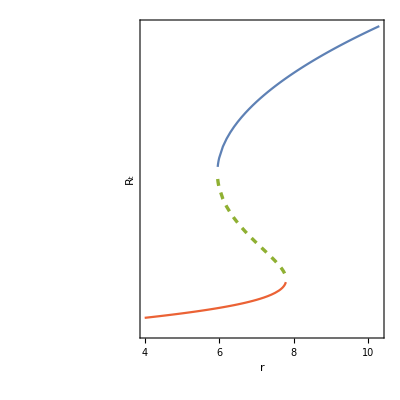

```mathematica
PlotRAhdI=Show[ListLinePlot[{RDown,RUp},PlotStyle->{ColorData[97,4],ColorData[97,1]},PlotStyle->Thickness[0.006]],ListLinePlot[RMiddle, PlotStyle->{ColorData[97,3],Dashed,Thickness[0.006]}],Frame->True,FrameLabel->{StyleForm["r",optsLabel1],StyleForm["R_t",optsLabel1]},FrameTicks->{{None, None},
{{{4,StyleForm["4",optsScale1],{0.03,0}},{6,StyleForm["6",optsScale1],{0.03,0}},{8,StyleForm["8",optsScale1],{0.03,0}},{10,StyleForm["10",optsScale1],{0.03,0}}},None}},Epilog->{Text[StyleForm["bistable",optsCentrality],{2,0.77},{0,0}],Text[StyleForm["s=0.02",optsCentrality],{1.97,0.86},{0,0}]},AspectRatio->1]
```

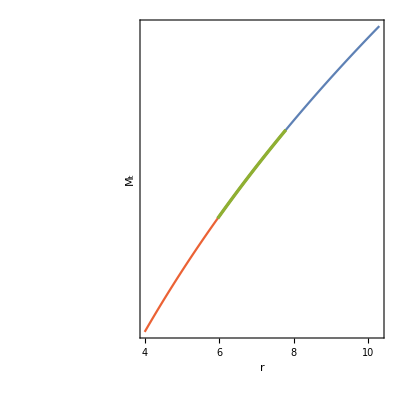

```mathematica
PlotMAhdI=Show[ListLinePlot[{MDown,MUp},PlotStyle->{ColorData[97,4],ColorData[97,1]},PlotStyle->Thickness[0.006]],ListLinePlot[MMiddle, PlotStyle->{ColorData[97,3],Thickness[0.006]}],Frame->True,FrameLabel->{StyleForm["r",optsLabel1],StyleForm["M_t",optsLabel1]},FrameTicks->{{None, None},
{{{4,StyleForm["4",optsScale1],{0.03,0}},{6,StyleForm["6",optsScale1],{0.03,0}},{8,StyleForm["8",optsScale1],{0.03,0}},{10,StyleForm["10",optsScale1],{0.03,0}}},None}},Epilog->{Text[StyleForm["bistable",optsCentrality],{2,0.77},{0,0}],Text[StyleForm["s=0.02",optsCentrality],{1.97,0.86},{0,0}]},AspectRatio->1]
```

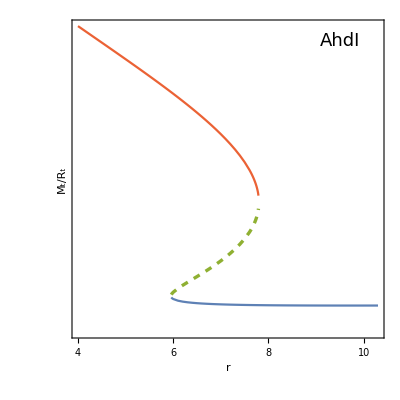

```mathematica
PlotMRAhdI=Show[ListLinePlot[{MRRatioDown,MRRatioUp},PlotStyle->{ColorData[97,4],ColorData[97,1]},PlotStyle->Thickness[0.006]],ListLinePlot[MRRatioMiddle, PlotStyle->{ColorData[97,3],Dashed,Thickness[0.006]}],Frame->True,FrameLabel->{StyleForm["r",optsLabel1],StyleForm["M_t/R_t",optsLabel1]},FrameTicks->{{None, None},
{{{4,StyleForm["4",optsScale1],{0.03,0}},{6,StyleForm["6",optsScale1],{0.03,0}},{8,StyleForm["8",optsScale1],{0.03,0}},{10,StyleForm["10",optsScale1],{0.03,0}}},None}
},Epilog->{Text[StyleForm["AhdI",optsCentrality],{9.5,0.95},{0,0}]},AspectRatio->1]
```

This now reproduces Figure 7 from the manuscript:

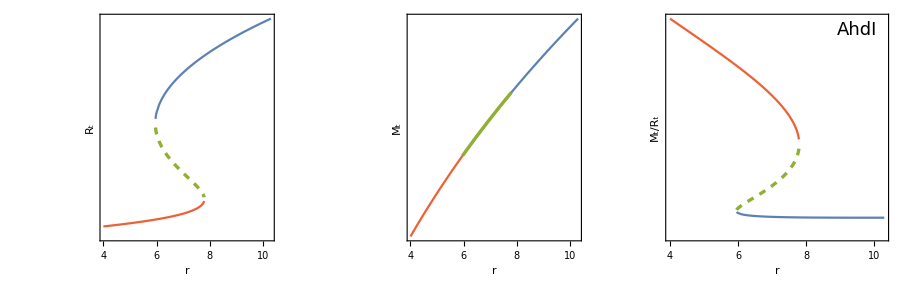

```mathematica
GraphicsRow[{PlotRAhdI,PlotMAhdI,PlotMRAhdI},ImageSize->900]
```